```mathematica
1+1
```

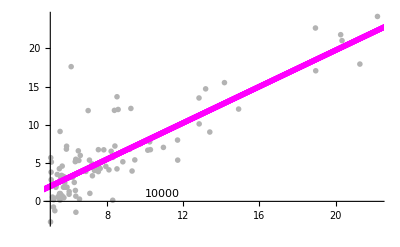
-Graphics-
{{-3.9614,1.1846}}

```mathematica
train[]
```

```mathematica
plotData[points_,color_]:=ListPlot[points,PlotStyle->Directive[color,PointSize[.01]],FrameTicks->False,PlotRangePadding->0.1,PlotRange->All];

plot2=plotData[List@@@datum,GrayLevel[0.7]];

plotSolution[net_,t_]:=Show[plot2,plotData[Transpose[{Range[-20,30,.02],net@Range[-20,30,.02]}],Magenta],Epilog->Text[t,{10,0.9},{-1,0}]];
```

```mathematica
plotMonotron[{b_,w_}]:=Plot[1*b+x w,{x,-4,30},PlotStyle->Magenta]
```

```mathematica
datumPlot2[{b_,w_}]:=Module[{error},
	error[{b_,w_}]=Total[#^2&/@((Last/@datum)-(yPred[{b,w}][#]&)/@(First/@datum))];
	Show[
	plot2,
	plotMonotron[{b,w}],
	Graphics[Text[Style[#,Red]&@("loss → "<>ToString[error]),{10,10}]]
	]]
```

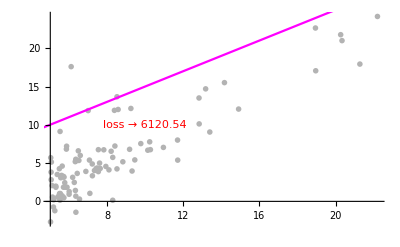

```mathematica
datumPlot2[{5,1}]
```

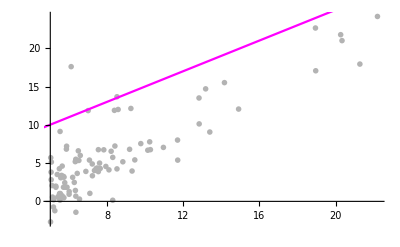

```mathematica
datumPlot[{5,1}]
```

```mathematica
Total[#^2&/@((Last/@datum)-(yPred[{5,1}][#]&)/@(First/@datum))]
```

6120.54

```mathematica
yPred[{b_,w_}][x_]:= b 1+w x ;
errorL2[{b_,w_}]:=Total[#^2&/@((Last/@datum)-(yPred[{b,w}][#]&)/@(First/@datum))];
```

```mathematica
RepeatedTiming[errorL2[{1,1}],2]
```

{0.00534,1991.7}

```mathematica
Clear[errorL2,createErrorFunction];createErrorFunction:=Module[{expr,ff},expr=(Expand[Total[#^2&/@((Last/@datum)-(yPred[{bSymbol,wSymbol}][#]&)/@(First/@datum))]]);
ff=Compile[{{bb, _Real},{ww,_Real}}, expr/.{bSymbol->bb,wSymbol->ww}];
errorL2[{b_,w_}]:=ff[b,w]
];
```

```mathematica
createErrorFunction
```

```mathematica
RepeatedTiming[errorL2[{1,1}],2]
```

{6.7×10^-6,1991.7}

```mathematica
Plot3D[errorL2[{x,y}],{x,-100,100},{y,-100,100}]
```

-Graphics3D-

```mathematica
expr
```

6222.11-1132.79 bSymbol+97 bSymbol^2-12673.8 wSymbol+1583. bSymbol wSymbol+7896.18 wSymbol^2

```mathematica
Compile
```

CompiledFunction[…]

```mathematica
RepeatedTiming[f[1,1]]
```

{6.28×10^-6,1991.7}